```mathematica
Clear[Evaluate[Context[]<>"*"]];
SetDirectory@NotebookDirectory[];
```

```mathematica
calRawDataCs=Import["data/137CsScale.dat.txt","Data"]⟦All,1⟧;
calRawDataCo=Import["data/60CoScale.dat.txt","Data"]⟦All,1⟧;
```

```mathematica
FindPeaks[calRawDataCs]//Select[460<#⟦1⟧<480&]
```

{{474,27783}}

```mathematica
FindPeaks[calRawDataCo,2]//Select[900<#⟦1⟧<1000&]
```

{{954,3915}}

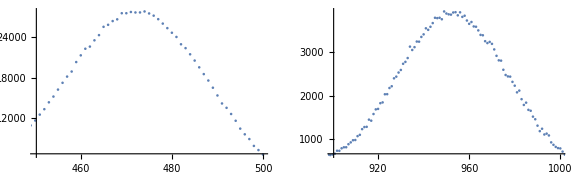

```mathematica
GraphicsRow[
ListPlot[#1,PlotRange->{#2,
MinMax@Extract[#1,Partition[Range@@#2,1]]}]&@@@{
{calRawDataCs,{450,500}},{calRawDataCo,{900,1000}}},
ImageSize->Large]
```

```mathematica
calData={{474,836,954},10^3*{.662,1.17,1.33}}ᵀ;calFunction=LinearModelFit[calData,x,x];
calFunction//Normal
```

1.68705+1.39441 x

```mathematica
calFunction["BestFitParameters"]//NumberForm[#,3]&//ScientificForm
calFunction["ParameterErrors"]//NumberForm[#,1]&//ScientificForm
calFunction["ParameterErrors"]/calFunction["BestFitParameters"]
```

{1.69,1.39}

{7.,9.×10^-3}

{4.32801,0.00669768}